```mathematica
y'[η]^2==1/3(r-3κ y[η]^2+λy[η]^4)
DSolve[%, y[η], η]
```

y'[η]^2==1/3 (r-3 κ y[η]^2+λy[η]^4)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[y'[η]^2==1/3 (r-3 κ y[η]^2+λy[η]^4),y[η],η]

```mathematica
Integrate[1/(x^2 Sqrt[λ/3+C/x^4]),x]
```

-((ⅈ 3^(1/4) √(3+(x^4 λ)/C) EllipticF[ⅈ ArcSinh[(x √((ⅈ √λ)/(√C)))/3^(1/4)],-1])/(x^2 √((ⅈ √λ)/(√C)) √((3 C)/x^4+λ)))

-((ⅈ 3^(1/4) √(3+(x^4 λ)/C) EllipticF[ⅈ ArcSinh[(x √((ⅈ √λ)/(√C)))/3^(1/4)],-1])/(x^2 √((ⅈ √λ)/(√C)) √((3 C)/x^4+λ)))

-((ⅈ √(3+(3 x^4 λ)/r) EllipticF[ⅈ ArcSinh[x √((ⅈ √λ)/(√r))],-1])/(x^2 √((ⅈ √λ)/(√r)) √(r/x^4+λ)))

1/(√(1+x^4))√(1+1/x^4) x^2 EllipticF[ⅈ ArcSinh[(-1)^(1/4) x],-1] Root-1.22-1.22 ⅈRoot[9+#1^4&,1]-1.224744871391589

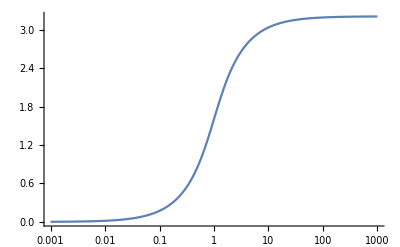

```mathematica
-((ⅈ 3^(1/4) √(3+(x^4 λ)/C) EllipticF[ⅈ ArcSinh[(x √((ⅈ √λ)/(√C)))/3^(1/4)],-1])/(x^2 √((ⅈ √λ)/(√C)) √((3 C)/x^4+λ)))
%/.{C->r/3}//FullSimplify
%/.{r->1, λ->1}//FullSimplify
LogLinearPlot[%,{x, 0.001, 1000}]
```

```mathematica
Integrate[1/(x^2 Sqrt[λ/3+C/x^4-κ/x^2]),x]
```

-((ⅈ √(3/2+(3 x^2 λ)/(-3 κ+√(9 κ^2-12 C λ))) √(1-(2 x^2 λ)/(3 κ+√(9 κ^2-12 C λ))) EllipticF[ⅈ ArcSinh[√2 x √(λ/(-3 κ+√(9 κ^2-12 C λ)))],(3 κ-√(9 κ^2-12 C λ))/(3 κ+√(9 κ^2-12 C λ))])/(x^2 √((3 C)/x^4-(3 κ)/x^2+λ) √(λ/(-3 κ+√(9 κ^2-12 C λ)))))

```mathematica
-((ⅈ √(3/2+(3 x^2 λ)/(-3 κ+√(9 κ^2-12 C λ))) √(1-(2 x^2 λ)/(3 κ+√(9 κ^2-12 C λ))) EllipticF[ⅈ ArcSinh[√2 x √(λ/(-3 κ+√(9 κ^2-12 C λ)))],(3 κ-√(9 κ^2-12 C λ))/(3 κ+√(9 κ^2-12 C λ))])/(x^2 √((3 C)/x^4-(3 κ)/x^2+λ) √(λ/(-3 κ+√(9 κ^2-12 C λ)))))
%/.{C->r/3}//FullSimplify
%/.{r->1, λ->1}//FullSimplify
Manipulate[LogLinearPlot[{%,1/(√(1+x^4))√(1+1/x^4) x^2 EllipticF[ⅈ ArcSinh[(-1)^(1/4) x],-1]},{x, 0.001, 1000}],{{κ,0},-2/3,2/3}]
```

-((ⅈ √(3/2+(3 x^2 λ)/(-3 κ+√(9 κ^2-12 C λ))) √(1-(2 x^2 λ)/(3 κ+√(9 κ^2-12 C λ))) EllipticF[ⅈ ArcSinh[√2 x √(λ/(-3 κ+√(9 κ^2-12 C λ)))],(3 κ-√(9 κ^2-12 C λ))/(3 κ+√(9 κ^2-12 C λ))])/(x^2 √((3 C)/x^4-(3 κ)/x^2+λ) √(λ/(-3 κ+√(9 κ^2-12 C λ)))))

-((ⅈ √(1-(2 x^2 λ)/(3 κ+√(9 κ^2-4 r λ))) √(6-(3 x^2 (3 κ+√(9 κ^2-4 r λ)))/r) EllipticF[ⅈ ArcSinh[√2 x √(λ/(-3 κ+√(9 κ^2-4 r λ)))],(9 κ^2-2 r λ-3 κ √(9 κ^2-4 r λ))/(2 r λ)])/(2 x^2 √(r/x^4-(3 κ)/x^2+λ) √(λ/(-3 κ+√(9 κ^2-4 r λ)))))

-((ⅈ √(1-(2 x^2)/(3 κ+√(-4+9 κ^2))) √(6-3 x^2 (3 κ+√(-4+9 κ^2))) EllipticF[ⅈ ArcSinh[√2 x √(1/(-3 κ+√(-4+9 κ^2)))],1/2 (-2+9 κ^2-3 κ √(-4+9 κ^2))])/(2 x^2 √(1+1/x^4-(3 κ)/x^2) √(1/(-3 κ+√(-4+9 κ^2)))))